# Farcaster Data

## Code

## Neynar Queries

General SQL Query where target fid is either Dan or Bot.

WITH ranked AS (
    SELECT  "fid", "target_fid", "type",
      ROW_NUMBER () OVER (
           PARTITION BY "fid", "target_fid"
            ORDER BY "timestamp" DESC
         ) AS rn
      FROM links
      WHERE "target_fid" = 3 -- 332281
  ),
followers_table AS (
      SELECT "fid" AS fid
        FROM ranked
        WHERE rn = 1 AND "type" = ' follow'
  ),
followers_followers _table AS (
      
      SELECT b . target_fid, COUNT(*) AS follower_count
          FROM
              followers_table a INNER JOIN links b ON a.fid = b.target_fid
          GROUP BY b.target_fid
    
    )
   SELECT follower_count
   FROM followers_followers_table 
   ORDER BY follower_count DESC

## Log Log Plot from Data

```mathematica
SeedRandom[1234];
```

```mathematica
GenerateLogLogPlot[dataset_] := Module[{data=dataset, A, B,pts, trimmed, powerLaw, indices, orderedIdx,n, sampledPlotPoints}, 
pts = Transpose[{Range[Length[data]],Normal[data]}];
n = Length[pts];
trimmed = Take[pts,Ceiling[0.2 *n]];
lm = {Log[#1],Log[#2]}&@@@trimmed//
LinearModelFit[#, x, x]&;
{A, B}=lm["BestFitParameters"];
powerLaw[x_]:=Exp[A] * x^B;

indices=RandomSample[Range[n],Ceiling[0.1*n]];
orderedIdx=Sort[indices];
sampledPlotPoints = pts[[orderedIdx]];

Show[
ListLogLogPlot[sampledPlotPoints,PlotMarkers->Automatic,AxesLabel->{"Rank","Value"},PlotLegends->{"Data"}],
LogLogPlot[powerLaw[x],{x,1, Length[pts]},PlotStyle->Thick,PlotLegends->{"Power‑Law Fit"}]
]
];
```

## User Data Analysis

### Dan Data

```mathematica
danData = Import["/home/jalil/Downloads/3955462_2025_04_21.csv", "Dataset", HeaderLines -> 1];
casterData = Import["/home/jalil/Downloads/3955426_2025_04_21.csv", "Dataset", HeaderLines -> 1];
```

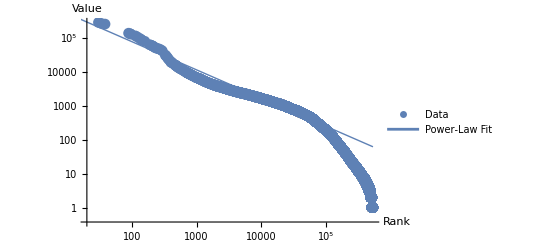

```mathematica
GenerateLogLogPlot[danData[[All, "follower_count"]]]
```

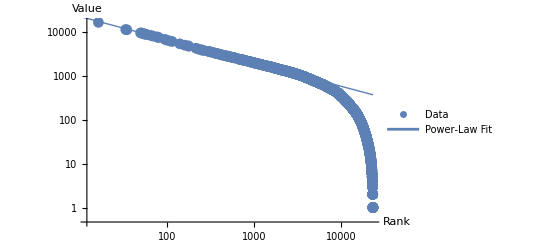

```mathematica
GenerateLogLogPlot[casterData[[All, "follower_count"]]]
```